# Project 1: Solving Kepler’s Equation

## Task 1:

```mathematica
Clear["Global`*"]
```

```mathematica
ke[x_] := x- ecc*Sin[x] -M; (*The equation we want to solve*)
keprime[x_]  := 1-ecc*Cos[x];
v={};
acc = 10^(-10);
maxi=50;
i=1;
For[ecc=0.1,ecc<=0.9,ecc=ecc+0.2, (*Loop through all the eccentricities*)
For[M=0,M<=2*Pi,M=M+Pi/20, (*Loop through the values of M*)
x0=M;
itnum = 0;
While[Abs[ke[x0]]>= acc, (*The Newton-Rapson Method, loop until accuracy is reached*)
x1=x0-ke[x0]/keprime[x0];
itnum = itnum+1;
x0=x1;
If[itnum==maxi, break[]]; (*If maximum number of iterations is reached we break the loop*) 
];
v =AppendTo[v,{M,x0}]; (*We create a table with all the pairs (M, E(M))*)
];
];

v= Partition[v,41];  (*Table splitting for all the different eccentricities*)
Print["The table of the values of the analytic solution"]
Print["Each line constists of the pairs (M,E(M)) for a certain value of eccentricity (e = 0.1, 0.3, 0.5, 0.7, 0.9)"]
Print[MatrixForm[v]]
```

The table of the values of the analytic solution

Each line constists of the pairs (M,E(M)) for a certain value of eccentricity (e = 0.1, 0.3, 0.5, 0.7, 0.9)

((0
0) | (π/20
0.174435) | (π/10
0.348288) | ((3 π)/20
0.521015) | (π/5
0.692137) | (π/4
0.861265) | ((3 π)/10
1.02811) | ((7 π)/20
1.19249) | ((2 π)/5
1.3543) | ((9 π)/20
1.51355) | (π/2
1.6703) | ((11 π)/20
1.82467) | ((3 π)/5
1.97683) | ((13 π)/20
2.12696) | ((7 π)/10
2.27531) | ((3 π)/4
2.4221) | ((4 π)/5
2.56758) | ((17 π)/20
2.712) | ((9 π)/10
2.85564) | ((19 π)/20
2.99875) | (π
π) | ((21 π)/20
3.28444) | ((11 π)/10
3.42754) | ((23 π)/20
3.57118) | ((6 π)/5
3.71561) | ((5 π)/4
3.86109) | ((13 π)/10
4.00788) | ((27 π)/20
4.15622) | ((7 π)/5
4.30636) | ((29 π)/20
4.45851) | ((3 π)/2
4.61288) | ((31 π)/20
4.76963) | ((8 π)/5
4.92888) | ((33 π)/20
5.0907) | ((17 π)/10
5.25508) | ((7 π)/4
5.42192) | ((9 π)/5
5.59105) | ((37 π)/20
5.76217) | ((19 π)/10
5.9349) | ((39 π)/20
6.10875) | (2 π
2 π)
(0
0) | (π/20
0.223603) | (π/10
0.442664) | ((3 π)/20
0.65367) | (π/5
0.854614) | (π/4
1.04485) | ((3 π)/10
1.22469) | ((7 π)/20
1.39493) | ((2 π)/5
1.55661) | ((9 π)/20
1.71078) | (π/2
1.85847) | ((11 π)/20
2.00059) | ((3 π)/5
2.13798) | ((13 π)/20
2.27138) | ((7 π)/10
2.40144) | ((3 π)/4
2.52875) | ((4 π)/5
2.65386) | ((17 π)/20
2.77725) | ((9 π)/10
2.89939) | ((19 π)/20
3.02069) | (π
π) | ((21 π)/20
3.26249) | ((11 π)/10
3.3838) | ((23 π)/20
3.50593) | ((6 π)/5
3.62932) | ((5 π)/4
3.75443) | ((13 π)/10
3.88175) | ((27 π)/20
4.01181) | ((7 π)/5
4.1452) | ((29 π)/20
4.28259) | ((3 π)/2
4.42472) | ((31 π)/20
4.5724) | ((8 π)/5
4.72658) | ((33 π)/20
4.88826) | ((17 π)/10
5.0585) | ((7 π)/4
5.23833) | ((9 π)/5
5.42857) | ((37 π)/20
5.62952) | ((19 π)/10
5.84052) | ((39 π)/20
6.05958) | (2 π
2 π)
(0
0) | (π/20
0.309253) | (π/10
0.593999) | ((3 π)/20
0.845336) | (π/5
1.06594) | (π/4
1.2617) | ((3 π)/10
1.43808) | ((7 π)/20
1.59935) | ((2 π)/5
1.74874) | ((9 π)/20
1.88867) | (π/2
2.02098) | ((11 π)/20
2.14711) | ((3 π)/5
2.26821) | ((13 π)/20
2.38519) | ((7 π)/10
2.49882) | ((3 π)/4
2.60975) | ((4 π)/5
2.71854) | ((17 π)/20
2.82569) | ((9 π)/10
2.93164) | ((19 π)/20
3.03681) | (π
π) | ((21 π)/20
3.24638) | ((11 π)/10
3.35155) | ((23 π)/20
3.45749) | ((6 π)/5
3.56464) | ((5 π)/4
3.67343) | ((13 π)/10
3.78436) | ((27 π)/20
3.898) | ((7 π)/5
4.01498) | ((29 π)/20
4.13607) | ((3 π)/2
4.26221) | ((31 π)/20
4.39452) | ((8 π)/5
4.53444) | ((33 π)/20
4.68383) | ((17 π)/10
4.8451) | ((7 π)/4
5.02148) | ((9 π)/5
5.21724) | ((37 π)/20
5.43785) | ((19 π)/10
5.68919) | ((39 π)/20
5.97393) | (2 π
2 π)
(0
0) | (π/20
0.480857) | (π/10
0.831347) | ((3 π)/20
1.09277) | (π/5
1.30345) | (π/4
1.48268) | ((3 π)/10
1.64077) | ((7 π)/20
1.78375) | ((2 π)/5
1.91547) | ((9 π)/20
2.03853) | (π/2
2.15479) | ((11 π)/20
2.2656) | ((3 π)/5
2.37203) | ((13 π)/20
2.47491) | ((7 π)/10
2.5749) | ((3 π)/4
2.67259) | ((4 π)/5
2.76845) | ((17 π)/20
2.86291) | ((9 π)/10
2.95636) | ((19 π)/20
3.04914) | (π
π) | ((21 π)/20
3.23405) | ((11 π)/10
3.32683) | ((23 π)/20
3.42027) | ((6 π)/5
3.51473) | ((5 π)/4
3.61059) | ((13 π)/10
3.70828) | ((27 π)/20
3.80828) | ((7 π)/5
3.91116) | ((29 π)/20
4.01758) | ((3 π)/2
4.1284) | ((31 π)/20
4.24465) | ((8 π)/5
4.36772) | ((33 π)/20
4.49944) | ((17 π)/10
4.64242) | ((7 π)/4
4.8005) | ((9 π)/5
4.97973) | ((37 π)/20
5.19041) | ((19 π)/10
5.45184) | ((39 π)/20
5.80233) | (2 π
2 π)
(0
0) | (π/20
0.807195) | (π/10
1.12696) | ((3 π)/20
1.34924) | (π/5
1.52747) | (π/4
1.68003) | ((3 π)/10
1.81564) | ((7 π)/20
1.93918) | ((2 π)/5
2.05372) | ((9 π)/20
2.16131) | (π/2
2.26342) | ((11 π)/20
2.36113) | ((3 π)/5
2.45528) | ((13 π)/20
2.54654) | ((7 π)/10
2.63545) | ((3 π)/4
2.72246) | ((4 π)/5
2.80798) | ((17 π)/20
2.89235) | ((9 π)/10
2.97589) | ((19 π)/20
3.05887) | (π
π) | ((21 π)/20
3.22431) | ((11 π)/10
3.3073) | ((23 π)/20
3.39083) | ((6 π)/5
3.4752) | ((5 π)/4
3.56072) | ((13 π)/10
3.64774) | ((27 π)/20
3.73665) | ((7 π)/5
3.82791) | ((29 π)/20
3.92206) | ((3 π)/2
4.01977) | ((31 π)/20
4.12188) | ((8 π)/5
4.22947) | ((33 π)/20
4.34401) | ((17 π)/10
4.46755) | ((7 π)/4
4.60315) | ((9 π)/5
4.75571) | ((37 π)/20
4.93395) | ((19 π)/10
5.15623) | ((39 π)/20
5.47599) | (2 π
2 π))

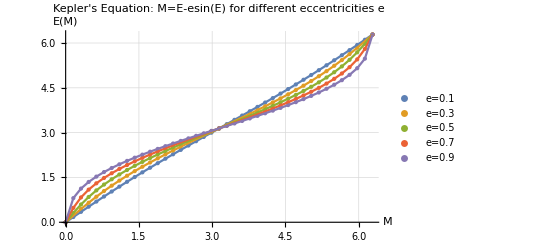

```mathematica
P1 =ListPlot[v, GridLines->Automatic,PlotStyle->PointSize[Medium],PlotLegends->{"e=0.1","e=0.3","e=0.5","e=0.7","e=0.9"},AxesOrigin->{0,0},AxesLabel->{"M","E(M)"},PlotLabel->"Kepler's Equation: M=E-esin(E)\n for different eccentricities e"];
P2 =ListLinePlot[v,PlotStyle->Thin, AxesOrigin->{0,0}];
Show[{P1,P2}]
```

## Task 2:

```mathematica
Clear[ecc,M]
f = Sin[M];
```

```mathematica
(*computation of the series expression E(M) by keeping terms up to order n=3*)
E3=M+ecc*Sin[M];
nmax=3;
For[n=2,n<=nmax,n++,
E3=E3+((ecc^n)/Factorial[n])*D[f^n,{M,n-1}];
]
```

```mathematica
(*computation of the series expression E(M) by keeping terms up to order n=3*)
E10=M+ecc*Sin[M];
nmax=10;
For[n=2,n<=nmax,n++,
E10=E10+((ecc^n)/Factorial[n])*D[f^n,{M,n-1}];
]
```

```mathematica
(*trigonometric reduction of the outcomes*)
E3S=Simplify[TrigReduce[E3]];
E10S=FullSimplify[TrigReduce[E10]];
Print["The trigonometric reducted series expression with terms up to n=3 is:", E3S]
Print["The trigonometric reducted series expression with terms up to n=10 is:", E10S]
```

The trigonometric reducted series expression with terms up to n=3 is:M+(ecc-ecc^3/8+ecc^2 Cos[M]) Sin[M]+3/8 ecc^3 Sin[3 M]

The trigonometric reducted series expression with terms up to n=10 is:M+1/92897280 ecc (126 (737280-92160 ecc^2+3840 ecc^4-80 ecc^6+ecc^8) Sin[M]+ecc (5376 (8640-2880 ecc^2+360 ecc^4-24 ecc^6+ecc^8) Sin[2 M]+ecc (-6804 (-5120+9 ecc^2 (320+9 ecc^2 (-8+ecc^2))) Sin[3 M]-98304 ecc (-315+252 ecc^2-84 ecc^4+16 ecc^6) Sin[4 M]+22500 ecc^2 (1344-1400 ecc^2+625 ecc^4) Sin[5 M]+279936 ecc^3 (112-144 ecc^2+81 ecc^4) Sin[6 M]-1058841 ecc^4 (-32+49 ecc^2) Sin[7 M]-4194304 ecc^5 (-9+16 ecc^2) Sin[8 M]+43046721 ecc^6 Sin[9 M]+50000000 ecc^7 Sin[10 M])))

```mathematica
(*computing the values of the series for 0<=M<=2pi and e=0.3*)
ecc=0.3;
Print["The trigonometric reducted series expression with terms up to n=3 and e=0.3 is:", E3S]
Print["The trigonometric reducted series expression with terms up to n=10 and e=0.3 is:", E10S]
```

The trigonometric reducted series expression with terms up to n=3 and e=0.3 is:M+(0.296625+0.09 Cos[M]) Sin[M]+0.010125 Sin[3 M]

The trigonometric reducted series expression with terms up to n=10 and e=0.3 is:M+3.22937×10^-9 (9.18561×10^7 Sin[M]+0.3 (4.50708×10^7 Sin[2 M]+0.3 (3.31082×10^7 Sin[3 M]+8.64059×10^6 Sin[4 M]+2.4767×10^6 Sin[5 M]+753530. Sin[6 M]+236629. Sin[7 M]+77052.7 Sin[8 M]+31381.1 Sin[9 M]+10935. Sin[10 M])))

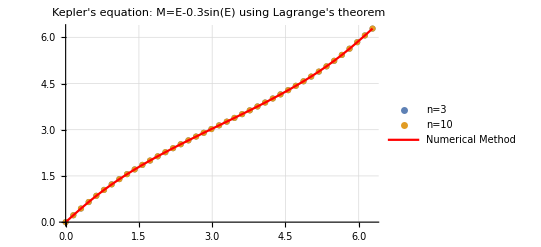

Βλέπουμε πως για εκκεντρότητα 0.3 η προσέγγιση του Lagrange συμπίπτει με την αριθμητική λύση

```mathematica
v03={};
For[M=0,M<=2*Pi,M=M+Pi/20,
xt3=N[E3S];
v03 = AppendTo[v03,{M,xt3}];
]
For[M=0,M<=2*Pi,M=M+Pi/20,
xt10=N[E10S];
v03=AppendTo[v03,{M,xt10}];(*We create a table with all the pairs (M, E(M))*)
]
v03= Partition[v03,41];(*Table splitting for the series until n=3 and n=10*)
(*Plot of the series method*)
P3=ListPlot[v03, GridLines->Automatic,PlotLegends->{"n=3","n=10"},PlotLabel->"Kepler's equation: M=E-0.3sin(E)\n using Lagrange's theorem"];
(*Plot of the numerical method*)
vv03 =Take[v,{2}];
P4 = ListLinePlot[vv03,PlotStyle->{Red}, PlotLegends->{"Numerical Method"}];
Show[{P3,P4}]
Print["Βλέπουμε πως για εκκεντρότητα 0.3 η προσέγγιση του Lagrange συμπίπτει με την αριθμητική λύση"]
```

```mathematica
Clear[ecc,xt3,xt10,M]
(*computing the values of the series for 0<=M<=2pi and e=0.9, the steps are the same as for e=0.3*)
v09={};
ecc=0.9;
Print["The trigonometric reducted series expression with terms up to n=3 and e=0.9 is:", E3S]
Print["The trigonometric reducted series expression with terms up to n=10 and e=0.9 is:", E10S]
```

The trigonometric reducted series expression with terms up to n=3 and e=0.9 is:M+(0.808875+0.81 Cos[M]) Sin[M]+0.273375 Sin[3 M]

The trigonometric reducted series expression with terms up to n=10 and e=0.9 is:M+9.68812×10^-9 (8.38036×10^7 Sin[M]+0.9 (3.5111×10^7 Sin[2 M]+0.9 (2.1564×10^7 Sin[3 M]+1.39336×10^7 Sin[4 M]+1.13006×10^7 Sin[5 M]+9.89839×10^6 Sin[6 M]-5.34229×10^6 Sin[7 M]-9.80771×10^6 Sin[8 M]+2.28768×10^7 Sin[9 M]+2.39148×10^7 Sin[10 M])))

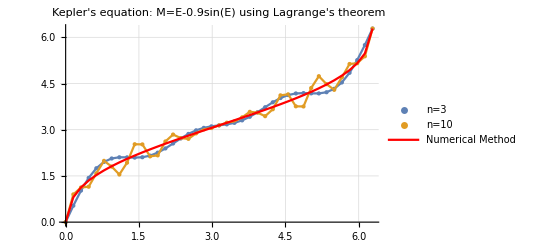

Βλέπουμε πως για εκκεντρότητα 0.9 η προσέγγιση του Lagrange δεν συμπίπτει με την αριθμητική λύση

Επιπλέον βλέπουμε πως όσο το n μεγαλώνει, τόσο περισσότερο η προσέγγιση αποκλίνει από την αριθμητική λύση

```mathematica
For[M=0,M<=2*Pi,M=M+Pi/20,
xt3=N[E3S];
v09 = AppendTo[v09,{M,xt3}];
]
For[M=0,M<=2*Pi,M=M+Pi/20,
xt10=N[E10S];
v09=AppendTo[v09,{M,xt10}];
]

v09= Partition[v09,41];

P5=ListPlot[v09,GridLines->Automatic,PlotStyle->PointSize[Medium],PlotLegends->{"n=3","n=10"},PlotLabel->"Kepler's equation: M=E-0.9sin(E)\n using Lagrange's theorem"];
P6=ListLinePlot[v09,PlotStyle->Thin];
vv09 =Take[v,{5}];
P7 = ListLinePlot[vv09,PlotStyle->{Red}, PlotLegends->{"Numerical Method"}];
Show[{P5,P6,P7}]
Print["Βλέπουμε πως για εκκεντρότητα 0.9 η προσέγγιση του Lagrange δεν συμπίπτει με την αριθμητική λύση"]
Print["Επιπλέον βλέπουμε πως όσο το n μεγαλώνει, τόσο περισσότερο η προσέγγιση αποκλίνει από την αριθμητική λύση"]
```

## Task 3:

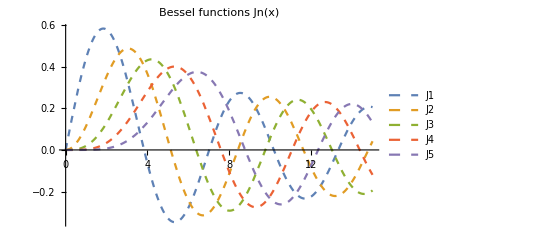

```mathematica
(*Creation of a function that represents the Bessel functions*)
J =Function[{n,y},Sum[(-1)^k/(Factorial[k]*Factorial[n+k])*(y/2)^(n+2*k),{k,0,Infinity}]];
Plot[{J[1,y],J[2,y],J[3,y],J[4,y],J[5,y]},{y,0,15},PlotLegends->{"J1","J2","J3","J4","J5"},PlotLabel->"Bessel functions Jn(x)",PlotStyle->Dashed]
```

```mathematica
Clear[ecc,M]
(*E(M) in terms of the a Fourier-Bessel series expansion: *)
EB = Function[{M,imax,ecc},M+Sum[2/i*J[i,i*ecc]*Sin[i*M],{i,1,imax}]];
Print["E(M) in terms up to j=3 of the a Fourier-Bessel series expansion "]
Print[EB[M,3,ecc]]
Print["E(M) in terms up to j=10 of the a Fourier-Bessel series expansion "]
Print[EB[M,10,ecc]]
```

E(M) in terms up to j=3 of the a Fourier-Bessel series expansion

M+2 BesselJ[1,ecc] Sin[M]+BesselJ[2,2 ecc] Sin[2 M]+2/3 BesselJ[3,3 ecc] Sin[3 M]

E(M) in terms up to j=10 of the a Fourier-Bessel series expansion

M+2 BesselJ[1,ecc] Sin[M]+BesselJ[2,2 ecc] Sin[2 M]+2/3 BesselJ[3,3 ecc] Sin[3 M]+1/2 BesselJ[4,4 ecc] Sin[4 M]+2/5 BesselJ[5,5 ecc] Sin[5 M]+1/3 BesselJ[6,6 ecc] Sin[6 M]+2/7 BesselJ[7,7 ecc] Sin[7 M]+1/4 BesselJ[8,8 ecc] Sin[8 M]+2/9 BesselJ[9,9 ecc] Sin[9 M]+1/5 BesselJ[10,10 ecc] Sin[10 M]

```mathematica
Print["E(M) in terms up to j=3 of the a Fourier-Bessel series expansion for e=0.3"]
Print[EB[M,3,0.3]]
Print["E(M) in terms up to j=10 of the a Fourier-Bessel series expansion for e=0.3"]
Print[EB[M,10,0.3]]
```

E(M) in terms up to j=3 of the a Fourier-Bessel series expansion for e=0.3

M+0.296638 Sin[M]+0.0436651 Sin[2 M]+0.00962269 Sin[3 M]

E(M) in terms up to j=10 of the a Fourier-Bessel series expansion for e=0.3

M+0.296638 Sin[M]+0.0436651 Sin[2 M]+0.00962269 Sin[3 M]+0.00251133 Sin[4 M]+0.000719769 Sin[5 M]+0.000218966 Sin[6 M]+0.0000694238 Sin[7 M]+0.000022689 Sin[8 M]+7.58942×10^-6 Sin[9 M]+2.58567×10^-6 Sin[10 M]

```mathematica
Print["E(M) in terms up to j=3 of the a Fourier-Bessel series expansion for e=0.9"]
Print[EB[M,3,0.9]]
Print["E(M) in terms up to j=10 of the a Fourier-Bessel series expansion for e=0.9"]
Print[EB[M,10,0.9]]
```

E(M) in terms up to j=3 of the a Fourier-Bessel series expansion for e=0.9

M+0.811899 Sin[M]+0.306144 Sin[2 M]+0.169364 Sin[3 M]

E(M) in terms up to j=10 of the a Fourier-Bessel series expansion for e=0.9

M+0.811899 Sin[M]+0.306144 Sin[2 M]+0.169364 Sin[3 M]+0.1099 Sin[4 M]+0.0778859 Sin[5 M]+0.0583823 Sin[6 M]+0.0454979 Sin[7 M]+0.0364845 Sin[8 M]+0.0299042 Sin[9 M]+0.0249388 Sin[10 M]

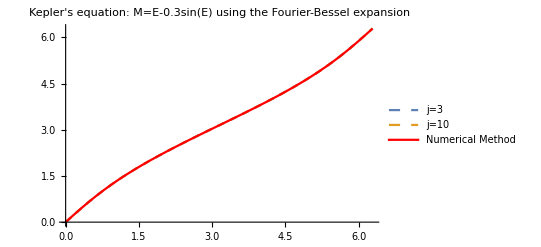

Βλέπουμε πως για εκκεντρότητα 0.3 η προσέγγιση Fourier-Bessel συμπίπτει και πάλι με την αριθμητική λύση

```mathematica
(*Plot of the results*)
P8 =Plot[{EB[M,3,0.3],EB[M,10,0.3]},{M,0,2*Pi},PlotStyle->Dashed,PlotLegends->{"j=3","j=10"},PlotLabel->"Kepler's equation: M=E-0.3sin(E)\n using the Fourier-Bessel expansion"];
Show[{P8,P4}]
Print["Βλέπουμε πως για εκκεντρότητα 0.3 η προσέγγιση Fourier-Bessel συμπίπτει και πάλι με την αριθμητική λύση"]
```

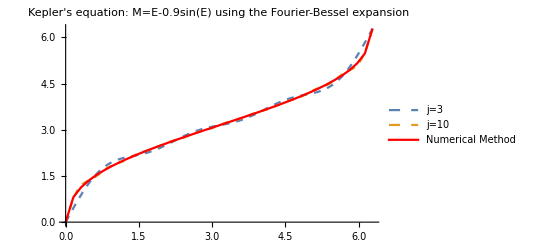

Βλέπουμε πως για εκκεντρότητα 0.9 η προσέγγιση Fourier-Bessel δεν συμπίπτει και πάλι με την αριθμητική λύση

Ωστόσο για j=10 η προσέγγιση γίνεται αρκετά καλύτερη

```mathematica
P9 = Plot[{EB[M,3,0.9],EB[M,10,0.9]},{M,0,2*Pi},PlotStyle->Dashed, PlotLegends->{"j=3","j=10"}, PlotLabel->"Kepler's equation: M=E-0.9sin(E)\n using the Fourier-Bessel expansion"];
Show[{P9,P7}]
Print["Βλέπουμε πως για εκκεντρότητα 0.9 η προσέγγιση Fourier-Bessel δεν συμπίπτει και πάλι με την αριθμητική λύση"]
Print["Ωστόσο για j=10 η προσέγγιση γίνεται αρκετά καλύτερη"]
```

```mathematica
Print["Παρατηρούμε πως μια κύρια διαφορά στις 2 σειρές είναι οι δυνάμεις των συντελεστών των τριγωνομετρικών όρων. Στην περίπτωση των σειρών Lagrange οι συντελεστές έχουν όλοι την ίδια τάξη μεγέθους όσο μεγαλώνει το όρισμα των τριγωνομετρικών όρων. Αντίθετα στην περίπτωση Bessel-Fourier οι συντελεστές όλο και μικραίνουν σε τάξη μεγέθους, όσο μεγαλώνουν τα ορίσματα των τριγωνομετρικών όρων. Ίσως αυτός να ναι ένας λόγος που για μεγάλη εκκεντρότητα, η λύση του Lagrange αποκλείνει όλο και περισσότερο από την αριθμητική λύση όσο μεγαλώνει ο αριθμός των όρων της σειράς. Αντίθετα στην λύση Bessel-Fourier με κάθε όρο προστίθενται μικρές διορθώσεις που βοηθούν στην όλο και καλύτερη προσέγγιση της αριθμητικής λύσης"]
```

Παρατηρούμε πως μια κύρια διαφορά στις 2 σειρές είναι οι δυνάμεις των συντελεστών των τριγωνομετρικών όρων. Στην περίπτωση των σειρών Lagrange οι συντελεστές έχουν όλοι την ίδια τάξη μεγέθους όσο μεγαλώνει το όρισμα των τριγωνομετρικών όρων. Αντίθετα στην περίπτωση Bessel-Fourier οι συντελεστές όλο και μικραίνουν σε τάξη μεγέθους, όσο μεγαλώνουν τα ορίσματα των τριγωνομετρικών όρων. Ίσως αυτός να ναι ένας λόγος που για μεγάλη εκκεντρότητα, η λύση του Lagrange αποκλείνει όλο και περισσότερο από την αριθμητική λύση όσο μεγαλώνει ο αριθμός των όρων της σειράς. Αντίθετα στην λύση Bessel-Fourier με κάθε όρο προστίθενται μικρές διορθώσεις που βοηθούν στην όλο και καλύτερη προσέγγιση της αριθμητικής λύσης